# Duopoly Retailers with Different Qualities

双寡头模型

```mathematica
ClearAll["`*"]
```

## 内置函数【单个和两个】

```mathematica
Qiujie1[profit_,var_]:=(firstor=D[profit,var]//FullSimplify;
Print["first order derivative is ",firstor];
equl=Solve[firstor==0,var]//FullSimplify;
Print["optimal solution is ",equl];
secondor=D[profit,{var,2}]//FullSimplify;
Print["second order derivative is ",secondor];
)
```

```mathematica
Qiujie2[profit1_,profit2_,var1_,var2_]:=
(firstor1=D[profit1,var1];
firstor2=D[profit2,var2];
secondor1=D[profit1,{var1,2}]//FullSimplify;
secondor2=D[profit2,{var2,2}]//FullSimplify;
Print["the secondor are",{secondor1,secondor2}];
Solve[{firstor1==0,firstor2==0},{var1,var2}]//FullSimplify
)
```

## 消费效用和利润（高质量和低质量）

## No MBGs

效用函数-Graphics-
这里分开了

```mathematica
NBNH=γH W-pNH;
NBNL=γL W-pNL;
```

```mathematica
Solve[NBNH==NBNL,W]
```

{{W→(pNH-pNL)/(γH-γL)}}

```mathematica
WNU=(pNH-pNL)/(γH-γL);
```

```mathematica
Solve[NBNL==0,W]
```

{{W→pNL/γL}}

```mathematica
WNL=pNL/γL;
```

画图

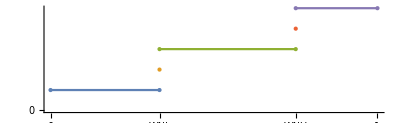

```mathematica
x1[pNL_:pNL,γL_:γL]:=pNL/γL;
x2[pNH_:pNH,pNL_:pNL,γL_:γL,γH_:γH]:=(pNH-pNL)/(γH-γL);
pNH=0.6;pNL=0.2;γH=0.8;γL=0.6;
data1={{Interval[{0,x1[]}],"No Buy"},{x1[],"x=WNU"},{Interval[{x1[],x2[]}],"Buy L"},{x2[],"x=WNL"},{Interval[{x2[],1}],"Buy H"}};
NumberLinePlot[data1[[All,1]],PlotLegends->data1[[All,-1]],Ticks->{{0,{x1[],"WNL"},{x2[],"WNU"},1}},Spacings->0.05]
Clear[pNH,pNL,γH,γL];
```

```mathematica
DNH=1-WNU
DNL=WNU-WNL
```

1-(pNH-pNL)/(γH-γL)

(pNH-pNL)/(γH-γL)-pNL/γL

-Graphics-

```mathematica
πNH[pNH_:pNH,pNL_:pNL]:=(1-(pNH-pNL)/(γH-γL))(pNH-cH);
πNL[pNH_:pNH,pNL_:pNL]:=((pNH-pNL)/(γH-γL)-pNL/γL)(pNL-cL);
```

## Op

```mathematica
Qiujie2[πNH[],πNL[],pNH,pNL]
```

the secondor are{2/(-γH+γL),(2 γH)/(γL (-γH+γL))}

{{pNH→(γH (2 cH+cL+2 γH-2 γL))/(4 γH-γL),pNL→(2 cL γH+(cH+γH-γL) γL)/(4 γH-γL)}}

-Graphics-  -Graphics-

```mathematica
pNHOp=(γH (2 cH+cL+2 γH-2 γL))/(4 γH-γL);
pNLOp=(2 cL γH+(cH+γH-γL) γL)/(4 γH-γL);
```

```mathematica
{πNHOp,πNLOp}={πNH[pNHOp,pNLOp],πNL[pNHOp,pNLOp]}//FullSimplify
```

{(γH (cL+2 γH-2 γL)+cH (-2 γH+γL))^2/((γH-γL) (-4 γH+γL)^2),(γH ((cH+γH-γL) γL+cL (-2 γH+γL))^2)/((γH-γL) γL (-4 γH+γL)^2)}

## With MBGs

```mathematica
NBGH=γH(W-pGH)-(1-γH)t;
NBGL=γL(W-pGL)-(1-γL)t;
```

```mathematica
Solve[NBGH==NBGL,W]//FullSimplify
```

{{W→pGL-t+((pGH-pGL) γH)/(γH-γL)}}

```mathematica
WGU=pGL-t+((pGH-pGL) γH)/(γH-γL);
```

```mathematica
Solve[NBGL==0,W]//FullSimplify
```

{{W→pGL+t (-1+1/γL)}}

```mathematica
WGL=pGL+t (-1+1/γL);
```

```mathematica
DGH=1-(pGL-t+((pGH-pGL) γH)/(γH-γL));
DGL=(pGL-t+((pGH-pGL) γH)/(γH-γL))-(pGL+t (-1+1/γL));
```

```mathematica
πGH[pGH_:pGH,pGL_:pGL]:=(1-(pGL-t+((pGH-pGL) γH)/(γH-γL)))(γH pGH-cH+(1-γH)(S-T))
πGL[pGH_:pGH,pGL_:pGL]:=((pGL-t+((pGH-pGL) γH)/(γH-γL))-(pGL+t (-1+1/γL)))(γL pGL-cL+(1-γL)(S-T))
```

## Op

```mathematica
Qiujie2[πGH[],πGL[],pGH,pGL]
```

the secondor are{(2 γH^2)/(-γH+γL),-(2 γH γL)/(γH-γL)}

{{pGH→(γH (2 cH+cL-3 S-t+3 T+2 (1+S+t-T) γH)+(t+(-2+S-2 t-T) γH) γL)/(γH (4 γH-γL)),pGL→(2 (cL-S-t+T) γH+(cH-S+2 t+T+(1+3 S+t-3 T) γH) γL-(1+t) γL^2)/((4 γH-γL) γL)}}

```mathematica
pGHOp=(γH (2 cH+cL-3 S-t+3 T+2 (1+S+t-T) γH)+(t+(-2+S-2 t-T) γH) γL)/(γH (4 γH-γL));
pGLOp=(2 (cL-S-t+T) γH+(cH-S+2 t+T+(1+3 S+t-3 T) γH) γL-(1+t) γL^2)/((4 γH-γL) γL);
```

```mathematica
{πGHOp,πGLOp}={πGH[pGHOp,pGLOp],πGL[pGHOp,pGLOp]}//FullSimplify
```

{(cL γH-(t+T-2 (1+t+T) γH+S (-1+2 γH)) (γH-γL)+cH (-2 γH+γL))^2/((γH-γL) (-4 γH+γL)^2),(γH (cH γL+cL (-2 γH+γL)-(γH-γL) (2 (t+T)+S (-2+γL)-(1+t+T) γL))^2)/((γH-γL) γL (-4 γH+γL)^2)}

## 比较

## 命题1-1 高质量寡头两种情况下的利润比较

```mathematica
πGHOp-πNHOp//FullSimplify
```

(-(γH (cL+2 γH-2 γL)+cH (-2 γH+γL))^2+(cL γH-(t+T-2 (1+t+T) γH+S (-1+2 γH)) (γH-γL)+cH (-2 γH+γL))^2)/((γH-γL) (-4 γH+γL)^2)

```mathematica
-(γH (cL+2 γH-2 γL)+cH (-2 γH+γL))^2+(cL γH-(t+T-2 (1+t+T) γH+S (-1+2 γH)) (γH-γL)+cH (-2 γH+γL))^2
```

```mathematica
cL γH-(t+T-2 (1+t+T) γH+S (-1+2 γH)) (γH-γL)+cH (-2 γH+γL)-(γH (cL+2 γH-2 γL)+cH (-2 γH+γL))//FullSimplify
```

(-S+t+T) (-1+2 γH) (γH-γL)

```mathematica
γH (cL+2 γH-2 γL)+cH (-2 γH+γL)+(cL γH-(t+T-2 (1+t+T) γH+S (-1+2 γH)) (γH-γL)+cH (-2 γH+γL))//FullSimplify
```

2 cL γH-(t+T-2 (2+t+T) γH+S (-1+2 γH)) (γH-γL)+2 cH (-2 γH+γL)

```mathematica
Reduce[2 cL γH-(t+T-2 (2+t+T) γH+S (-1+2 γH)) (γH-γL)+2 cH (-2 γH+γL)>0&&1>γH>γL>0&&cH>0&&cL>0&&S-T-t>0&&γH>1/2&&t>0&&T>0]
```

(0<γL≤1/2&&1/2<γH<1&&T>0&&t>0&&((t+T<S≤(-t-T+4 γH+2 t γH+2 T γH)/(-1+2 γH)&&cL>0&&0<cH<(2 cL γH+S γH-t γH-T γH+4 γH^2-2 S γH^2+2 t γH^2+2 T γH^2-S γL+t γL+T γL-4 γH γL+2 S γH γL-2 t γH γL-2 T γH γL)/(4 γH-2 γL))||(S>(-t-T+4 γH+2 t γH+2 T γH)/(-1+2 γH)&&cL>(-S γH+t γH+T γH-4 γH^2+2 S γH^2-2 t γH^2-2 T γH^2+S γL-t γL-T γL+4 γH γL-2 S γH γL+2 t γH γL+2 T γH γL)/(2 γH)&&0<cH<(2 cL γH+S γH-t γH-T γH+4 γH^2-2 S γH^2+2 t γH^2+2 T γH^2-S γL+t γL+T γL-4 γH γL+2 S γH γL-2 t γH γL-2 T γH γL)/(4 γH-2 γL))))||(1/2<γL<1&&γL<γH<1&&T>0&&t>0&&((t+T<S≤(-t-T+4 γH+2 t γH+2 T γH)/(-1+2 γH)&&cL>0&&0<cH<(2 cL γH+S γH-t γH-T γH+4 γH^2-2 S γH^2+2 t γH^2+2 T γH^2-S γL+t γL+T γL-4 γH γL+2 S γH γL-2 t γH γL-2 T γH γL)/(4 γH-2 γL))||(S>(-t-T+4 γH+2 t γH+2 T γH)/(-1+2 γH)&&cL>(-S γH+t γH+T γH-4 γH^2+2 S γH^2-2 t γH^2-2 T γH^2+S γL-t γL-T γL+4 γH γL-2 S γH γL+2 t γH γL+2 T γH γL)/(2 γH)&&0<cH<(2 cL γH+S γH-t γH-T γH+4 γH^2-2 S γH^2+2 t γH^2+2 T γH^2-S γL+t γL+T γL-4 γH γL+2 S γH γL-2 t γH γL-2 T γH γL)/(4 γH-2 γL))))

```mathematica
Manipulate[πGHOp-πNHOp,{}]
```

实际上这里没看出个啥

## 命题1-1 低质量寡头两种情况下的利润比较

```mathematica
πGLOp-πNLOp//FullSimplify
```

(γH (-((cH+γH-γL) γL+cL (-2 γH+γL))^2+(cH γL+cL (-2 γH+γL)-(γH-γL) (2 (t+T)+S (-2+γL)-(1+t+T) γL))^2))/((γH-γL) γL (-4 γH+γL)^2)

## 命题1-2